```mathematica
indexVector[n_]:=Tuples[{0,1},n]
quardicM[m_,v_]:=(m.v).v
```

```mathematica
cheegerCut[G_]:=Module[{n1 ,L,DM,iv,cutValue,
l,Result},
n1 = Length[VertexList[G]];
L=KirchhoffMatrix[G];
DM=L *IdentityMatrix[Length[VertexList[G]]];
iv=Table[1,{i,1,n1}];
cutValue=(quardicM[L,#]/Min[quardicM[DM,#],quardicM[DM,iv-#]]&);
l=DeleteElements[indexVector[n1],{Table[1,n1],Table[0,n1]}];
Result=(MinimalBy[l,cutValue])[[1]];
{Result,cutValue[Result]}

]
```

```mathematica
lambda[G_]:=Module[{L,DM},L=KirchhoffMatrix[G];DM=L *IdentityMatrix[Length[VertexList[G]]];
Map[First,N[Eigensystem[{L,DM},-2]]]]
```

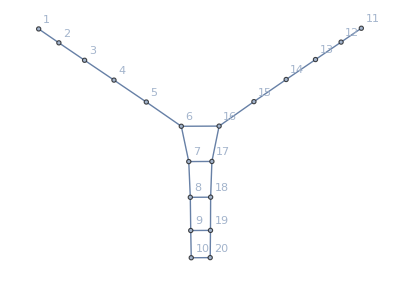

{0.0424405,{-863.771,-827.112,-720.247,-552.247,-337.371,-93.8591,-26.1149,-7.27565,-2.0613,-0.707107,863.771,827.112,720.247,552.247,337.371,93.8591,26.1149,7.27565,2.0613,0.707107}}

{{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,1,1,1},1/11}

```mathematica
G=Graph[Join[
Table[i<->i+1,{i,1,9}],
Table[i<->i+1,{i,11,19}],
Table[i<->i+10,{i,6,10}]
],VertexLabels->"Name"]
lambda[G]
cheegerCut[G]
```